## Задача 1

```mathematica
Ens = Range[-0.1, 0.1, 0.02];
sols=Map[NDSolveValue[{(-ψ''[r])/(2*m)+(l(l+1))/(2*m*r^2)ψ[r]-q/r ψ[r]==# ψ[r],ψ[0.1]== 1,ψ'[0.1]== 0},ψ[x],{r,0.1,30}]&, Ens];
```

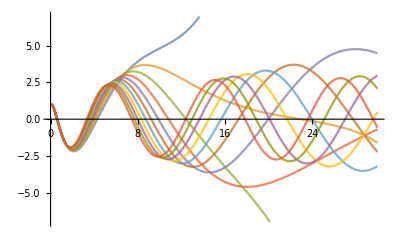

```mathematica
(*Manipulate[*)
q=1;
l=0;
m=1;
Plot[sols,{x,0.1,30}, PlotRange->{Automatic, {-7, 7}}, PlotStyle->Opacity[0.75]]
(*{{En, -0.05},-0.1,0}]*)
```

## Задача 2

```mathematica
(* задаем отображение элементов алгебры *)
$PrePrint= (Expand[#]/.{F[a_] :> x^a})&;
```

```mathematica
(* правила раскрытия F *)
ClearAll[F];
Times[F[a_],F[b_] ] ^:= F[a+b];
Power[F[a_], n_] ^:= F[a n];
F[a_/; a >= 2] := Expand[(-F[0])^Quotient[a, 2] F[Mod[a, 2]]];
```

```mathematica
(* примеры *)
F[3] 
F[4] 
F[0]  + F[5]
```

-x

1

1+x

```mathematica
(F[2] + F[4]F[5])^10
```

-32 x

## Задача 4

```mathematica
ClearAll[HamEq];
HamEq[H_,coord_]:= Module[{n,i,rules1,rules2,equations,L1,L2},
n=Length[coord];
equations=Table[0,{i1,n},{j1,2}];
For[i=1,i≤n,i++,
equations[[i,1]]=- D[H,coord[[i,1]][t] ];
equations[[i,2]]= D[H,coord[[i,2]][t] ]
];
equations
];
```

```mathematica
H0=p1[t]^2/(2m1)+p2[t]^2/(2m2)+p3[t]^2/(2m3)+U1[q1[t]^2 + q2[t]^2 + q3[t]^2] + U[q2[t]];
eq2=HamEq[H0,{{q1,p1},{q2,p2},{q3,p3}}];
TableForm@Transpose@eq2
```

-2 q1[t] U1'[q1[t]^2+q2[t]^2+q3[t]^2] | -U'[q2[t]]-2 q2[t] U1'[q1[t]^2+q2[t]^2+q3[t]^2] | -2 q3[t] U1'[q1[t]^2+q2[t]^2+q3[t]^2]
p1[t]/m1 | p2[t]/m2 | p3[t]/m3